-0.29862+0. ⅈ

(0.0626486+0. ⅈ)/((0.0626486+2.46373×10^-18 ⅈ)+(0.407966+1.38778×10^-17 ⅈ) s+(0.548937+2.46373×10^-18 ⅈ) s^2+(1.41503+1.38778×10^-17 ⅈ) s^3+(0.5745+0. ⅈ) s^4+s^5)

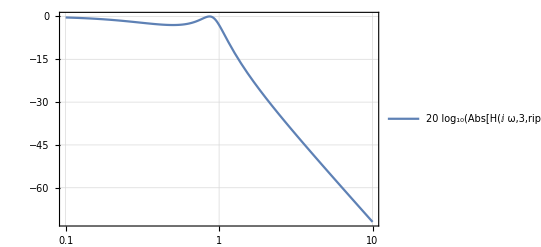

###### m = 2 ######

{{-0.32245+0.777158 ⅈ,-0.32245-0.777158 ⅈ}}

--------

{(1.+0. ⅈ)+(0.910942+0. ⅈ) s+(1.41253+0. ⅈ) s^2}

###### m = 3 ######

{{-0.14931+0.903814 ⅈ,-0.14931-0.903814 ⅈ},{-0.29862+0. ⅈ,-0.29862+0. ⅈ}}

--------

{(1.+0. ⅈ)+(0.35585+0. ⅈ) s+(1.19165+0. ⅈ) s^2}

------(-1.+0. ⅈ)-(3.34874+0. ⅈ) s

###### m = 4 ######

{{-0.0851704+0.946484 ⅈ,-0.0851704-0.946484 ⅈ},{-0.20562+0.392047 ⅈ,-0.20562-0.392047 ⅈ}}

--------

{(1.+0. ⅈ)+(0.188621+0. ⅈ) s+(1.10731+0. ⅈ) s^2,(1.-1.11022×10^-16 ⅈ)+(2.09837+0. ⅈ) s+(5.10256+0. ⅈ) s^2}

###### m = 5 ######

{{-0.0548599+0.965927 ⅈ,-0.0548599-0.965927 ⅈ},{-0.143625+0.596976 ⅈ,-0.143625-0.596976 ⅈ},{-0.17753+0. ⅈ,-0.17753+0. ⅈ}}

--------

{(1.+0. ⅈ)+(0.117219+0. ⅈ) s+(1.06835+0. ⅈ) s^2,(1.+0. ⅈ)+(0.761919+0. ⅈ) s+(2.65246+0. ⅈ) s^2}

------(-1.+0. ⅈ)-(5.63284+0. ⅈ) s

###### m = 6 ######

{{-0.0382295+0.976406 ⅈ,-0.0382295-0.976406 ⅈ},{-0.104445+0.714779 ⅈ,-0.104445-0.714779 ⅈ},{-0.142674+0.261627 ⅈ,-0.142674-0.261627 ⅈ}}

--------

{(1.+0. ⅈ)+(0.080076+0. ⅈ) s+(1.04731+0. ⅈ) s^2,(1.-2.77556×10^-17 ⅈ)+(0.400312+0. ⅈ) s+(1.91638+0. ⅈ) s^2,(1.+5.55112×10^-17 ⅈ)+(3.21322+0. ⅈ) s+(11.2607+0. ⅈ) s^2}

```mathematica
p[m_,k_,ϵ_]:=-Sinh[1/m ArcSinh[1/ϵ]]Sin[π/2*(2k+1)/m]+ⅈ Cosh[1/m ArcSinh[1/ϵ]]Cos[π/2*(2k+1)/m];
ϵ[dB_]:=√(10^(0.1*dB)-1);
H[s_,m_,dB_]:=(∏_(k=0)^(m-1) (-p[m,k,ϵ[dB]]))/(∏_(k=0)^(m-1) (s-p[m,k,ϵ[dB]]));
(*=============*)
rip=3;(* Unit: dB *)
p[3,1,ϵ[rip]]
ExpandAll[H[s,5,rip]]
LogLinearPlot[20*Log10[Abs[H[ⅈ ω,3,rip]]],{ω,0.1,10},PlotTheme->"Detailed"]
(*-----------*)
For[m=2,m≤6,m++,
Print["###### m = ",m," ######"];
Print[N[Table[{p[m,k,ϵ[rip]],p[m,m-1-k,ϵ[rip]]},{k,0,Ceiling[m/2]-1}]]];
Print["--------"];
Print[Table[
ExpandAll[((s-p[m,k,ϵ[rip]])(s-p[m,m-1-k,ϵ[rip]]))/(p[m,k,ϵ[rip]]*p[m,m-1-k,ϵ[rip]])]
,{k,0,Floor[m/2]-1}]];
If[Mod[m,2]==1,
Print["------",ExpandAll[(s-p[m,Floor[m/2],ϵ[rip]])/(p[m,Floor[m/2],ϵ[rip]])]]
,];
]
```

```mathematica
ϵ[0.5]
```

0.349311

```mathematica
ClearAll[m,k,ϵ];
Normalize[p[m,k,ϵ]]
FullSimplify[Abs[p[m,k,ϵ]],Assumptions->{m,k,ϵ}∈Reals]
```

(ⅈ Cos[((1+2 k) π)/(2 m)] Cosh[ArcSinh[1/ϵ]/m]-Sin[((1+2 k) π)/(2 m)] Sinh[ArcSinh[1/ϵ]/m])/Norm[ⅈ Cos[((1+2 k) π)/(2 m)] Cosh[ArcSinh[1/ϵ]/m]-Sin[((1+2 k) π)/(2 m)] Sinh[ArcSinh[1/ϵ]/m]]

Abs[Cos[(π+2 k π-2 ⅈ ArcCsch[ϵ])/(2 m)]]

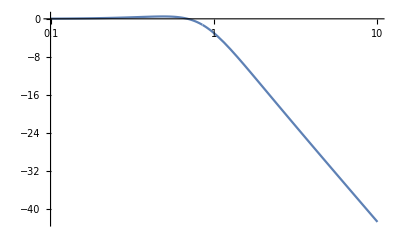

```mathematica
LogLinearPlot[20*Log10[Abs[1/(1+1.3614ⅈ ω+1.3827(ⅈ ω)^2)]],{ω,0.1,10}]
```